```mathematica
(*Inputs*)
g=1.5;
κ=0.2;
Get["/scratch/network/zz3250/Wolfram Mathematica/SG_SS_Kappa0p2G1p5_N50000"];
PhiVSYKappa0p2G1p5=Interpolation[FinalPhiList,InterpolationOrder->4];
ϕss[x_]:=PhiVSYKappa0p2G1p5[(π^(1/2)*Exp[(2 π*κ)^(1/2) x])/(1+Exp[(2 π*κ)^(1/2) x])];data=Table[{x,ϕss[x]},{x,-150,150,0.001}];
ϕssint=Interpolation[data];
intermediatePhi[x_]:=2*Sqrt[π]*ϕssint[x];
cosTerm[x_]:=Cos[intermediatePhi[x]];
potentialhamiltonian[x_]:=2*Pi*κ*cosTerm[x]+g^2;
```

```mathematica
L=200;
dx=.01;
total=200;
H1=-u''[x]+Evaluate[potentialhamiltonian[x]]*u[x];
{vals,fns}=NDEigensystem[{H1,DirichletCondition[u[x]==0,True]},u[x],{x,-L/2,L/2},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->dx}},"Arnoldi","MaxIterations"->7000,"BasisSize"->total+1,"Shift"->2.63}];
```

```mathematica
xRange=Range[-100,100,dx];
originalData=Table[{x,-fns[[1]]/. x->x},{x,xRange}];
ϕb=Interpolation[originalData];
```

```mathematica
(*Testing to find k2b*)
2*Sqrt[vals[[1]]]
Sqrt[vals[[177]]]
```

3.35569

3.35032

```mathematica
(*Setting up constants*)
k2b=177;
ωk=Sqrt[vals[[k2b]]];
tildek2b=Sqrt[ωk^2-g^2-2*Pi*κ];
λ3=2*Pi^(3/2);
λ4=4*Pi^2/3;
ωb=Sqrt[vals[[1]]];
ϕk2b=(1/Sqrt[2])*(fns[[k2b+1]]+I*fns[[k2b]]);
Vbb2b=NIntegrate[Sin[intermediatePhi[x]]*fns[[1]]*fns[[1]]*ϕk2b,{x,-100,100}];
Vbbbb=NIntegrate[Cos[intermediatePhi[x]]*fns[[1]]^4,{x,-100,100}];
```

```mathematica
Acoeff=I*λ3/(2*tildek2b*Sqrt[ωb])*Vbb2b
Bcoeff=λ3^2/(32*ωb^3)*Abs[Vbb2b]^2
Ccoeff=I*3*λ4/(8*ωb^2)*Vbbbb
```

4.36503×10^-6-0.0438842 ⅈ

0.000659976

0.-0.114787 ⅈ

```mathematica
Nb=4; (*Max occupation for b mode*)
Nk=1; (*Max occupation for k mode*)
```

```mathematica
(*Generate all b,k pairs*)
states=Flatten[Table[{b,k},{b,0,Nb},{k,0,Nk}],1]
nStates=Length[states]
```

{{0,0},{0,1},{1,0},{1,1},{2,0},{2,1},{3,0},{3,1},{4,0},{4,1}}

10

```mathematica
varsSig=Table[sig[i,j],{i,nStates},{j,nStates}];
varsA=Table[aa[i,j],{i,nStates},{j,nStates}];
varsH=Table[hh[i,j],{i,nStates},{j,nStates}];
```

```mathematica
(*Definition of ak2b(0)*)
matAk2b=Table[If[states[[i,1]]==states[[j,1]]&&states[[i,2]]==states[[j,2]]-1,Sqrt[states[[j,2]]],0],{i,nStates},{j,nStates}];
MatrixForm[matAk2b]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*Definition of H at t=0*)
initH=Table[If[i==j,states[[i,1]]+1/2,0],{i,nStates},{j,nStates}];
MatrixForm[initH]
```

(1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 5/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 7/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9/2)

```mathematica
(*Definition of a at t=0*)
initA=Table[If[states[[i,1]]==states[[j,1]]-1&&states[[i,2]]==states[[j,2]],Sqrt[states[[j,1]]],0],{i,nStates},{j,nStates}];
MatrixForm[initA]
```

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | √2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | √2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | √3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | √3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*Definition of sigma at t=0*)
initSig=Table[0,{i,nStates},{j,nStates}];
MatrixForm[initSig]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*EOMs*)
eqs=Flatten[{Table[varsSig[[i,j]]'[t]==Sum[varsA[[i,n]][t]*varsA[[n,j]][t],{n,nStates}],{i,nStates},{j,nStates}],Table[varsA[[i,j]]'[t]==Sum[Acoeff*Conjugate[varsA[[n,i]][t]]*matAk2b[[n,j]]-Bcoeff*(Conjugate[varsA[[n,i]][t]]*varsSig[[n,j]][t]+varsSig[[i,n]][t]*Conjugate[varsA[[j,n]][t]])+Ccoeff*(varsH[[i,n]][t] *varsA[[n,j]][t]+varsA[[i,n]][t] *varsH[[n,j]][t]),{n,nStates}],{i,nStates},{j,nStates}],Table[varsH[[i,j]]'[t]==Sum[Acoeff*Conjugate[varsA[[n,i]][t]]*Conjugate[varsA[[m,n]][t]]*matAk2b[[m,j]]+Conjugate[Acoeff]*Conjugate[matAk2b[[n,i]]]*varsA[[n,m]][t]*varsA[[m,j]][t]-Bcoeff*(varsA[[i,n]][t]*Conjugate[varsSig[[m,n]][t]]*varsA[[m,j]][t]+Conjugate[varsA[[n,i]][t]]*varsSig[[n,m]][t]*Conjugate[varsA[[j,m]][t]]+Conjugate[varsSig[[n,i]][t]]*varsA[[n,m]][t]*varsA[[m,j]][t]+Conjugate[varsA[[n,i]][t]]*Conjugate[varsA[[m,n]][t]]*varsSig[[m,j]][t]),{n,nStates},{m,nStates}],{i,nStates},{j,nStates}]}];
```

```mathematica
(*Initial conditions*)
ics=Flatten[{Table[varsSig[[i,j]][0]==initSig[[i,j]],{i,nStates},{j,nStates}],Table[varsA[[i,j]][0]==initA[[i,j]],{i,nStates},{j,nStates}],Table[varsH[[i,j]][0]==initH[[i,j]],{i,nStates},{j,nStates}]}];
```

```mathematica
sol=NDSolve[{eqs,ics},Flatten[{varsSig,varsA,varsH}],{t,0,100}];
```

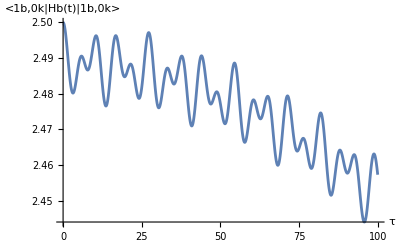

```mathematica
Plot[hh[5,5][t]/.sol,{t,0,100},
AxesLabel->{"τ","<2b,0k|Hb(t)|2b,0k>"}]
```